```mathematica
(* Notebook for solving the NEM relay ODE numerically *)
(* Mostly useful for validating transient behavior *)
ClearAll["Global`*"]
```

```mathematica
(* Relay parameters *)
k=Quantity[26.27, ("Newtons")/("Meters")]; (* spring constant *)
m=Quantity[1.052×10^-14, "Kilograms"]; (* relay proof mass *)
ω0=Quantity[9.066167477593858×10^6, "Hertz"]; (* first eigenfrequency *)
Q=10000000000; (* damping coefficient *)
W=Quantity[3, "Micrometers"]; (* relay plate width *)
L=Quantity[3, "Micrometers"]; (* relay plate length *)
gact=Quantity[60, "Nanometers"]; (* actuation gap *)
tsp=Quantity[0.03, "Micrometers"]; (* dielectric spacer thickness *)
Ksp=5.7; (* dielectric constant of spacer *)
geff=gact+tsp /Ksp; (* effective actuation gap *)
```

```mathematica
(* Driving parameters *)
Vgbtran=Quantity[5, "Volts"]; (* gate-to-body voltage for transient *)
```

```mathematica
(* NEM relay ODE and initial conditions *)
(* z in units of m, t in units of s *)
ode=z''[t]Quantity[, ("Meters")/("Seconds")^2]==(Quantity[, "ElectricConstant"] (W L) Vgb^2)/(2 (geff-z[t]Quantity[, "Meters"])^2 m)-ω0/Q z'[t]Quantity[, ("Meters")/("Seconds")]+ω0^2 z[t]Quantity[, "Meters"] ;
eqns={ode,z[0]==0,z'[0]==0};
result=NDSolve[eqns/.{Vgb->Vgbtran},z[t],{t,0,2×10^-7}]
```

NDSolve::ndsz: At t == 5.97354×10^-8, step size is effectively zero; singularity or stiff system suspected.

{{z[t]→InterpolatingFunction[…][t]}}

InterpolatingFunction[…][t]

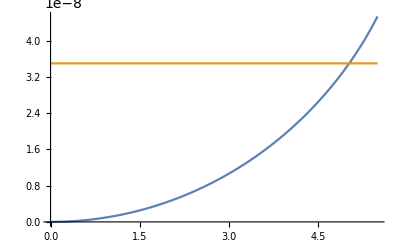

{t→4.91781×10^-8}

```mathematica
(* Plot transient displacement *)
tfn=z[t]/.result[[1]]
Plot[{tfn,3.5×10^-8},{t,0,5.5×10^-8}]
FindRoot[tfn==3.5×10^-8,{t,0,5.5×10^-8}]
```